# (5) Dimension Reduction

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../cSrc/";
```

## Get data for one behavior

```mathematica
aa1=Import[StringJoin[dir,"A_avoid_n1.dat"]];
aa2=Import[StringJoin[dir,"A_avoid_n2.dat"]];
aa3=Import[StringJoin[dir,"A_avoid_n3.dat"]];
aa4=Import[StringJoin[dir,"A_avoid_n4.dat"]];
aa5=Import[StringJoin[dir,"A_avoid_n5.dat"]];
aa6=Import[StringJoin[dir,"A_avoid_n6.dat"]];
aa7=Import[StringJoin[dir,"A_avoid_n7.dat"]];
ac1=Import[StringJoin[dir,"A_approach_n1.dat"]];
ac2=Import[StringJoin[dir,"A_approach_n2.dat"]];
ac3=Import[StringJoin[dir,"A_approach_n3.dat"]];
ac4=Import[StringJoin[dir,"A_approach_n4.dat"]];
ac5=Import[StringJoin[dir,"A_approach_n5.dat"]];
ac6=Import[StringJoin[dir,"A_approach_n6.dat"]];
ac7=Import[StringJoin[dir,"A_approach_n7.dat"]];
```

```mathematica
ba1=Import[StringJoin[dir,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir,"B_avoid_n5.dat"]];
ba6=Import[StringJoin[dir,"B_avoid_n6.dat"]];
ba7=Import[StringJoin[dir,"B_avoid_n7.dat"]];
bc1=Import[StringJoin[dir,"B_approach_n1.dat"]];
bc2=Import[StringJoin[dir,"B_approach_n2.dat"]];
bc3=Import[StringJoin[dir,"B_approach_n3.dat"]];
bc4=Import[StringJoin[dir,"B_approach_n4.dat"]];
bc5=Import[StringJoin[dir,"B_approach_n5.dat"]];
bc6=Import[StringJoin[dir,"B_approach_n6.dat"]];
bc7=Import[StringJoin[dir,"B_approach_n7.dat"]];
```

```mathematica
d1 = Flatten[{aa1,ac1,ba1,bc1}];
d2 = Flatten[{aa2,ac2,ba2,bc2}];
d3 = Flatten[{aa3,ac3,ba3,bc3}];
d4 = Flatten[{aa4,ac4,ba4,bc4}];
d5 = Flatten[{aa5,ac5,ba5,bc5}];
d6 = Flatten[{aa6,ac6,ba6,bc6}];
d7 = Flatten[{aa7,ac7,ba7,bc7}];
vectors =Transpose[{d1,d2,d3,d4,d5,d6,d7}];
```

## Dimension Reduction 2D

```mathematica
dr=DimensionReduction[vectors,2];
```

```mathematica
ba = Table[dr[Transpose[{ba1[[x]],ba2[[x]],ba3[[x]],ba4[[x]],ba5[[x]],ba6[[x]],ba7[[x]]}]],{x,1,100}];
bc = Table[dr[Transpose[{bc1[[x]],bc2[[x]],bc3[[x]],bc4[[x]],bc5[[x]],bc6[[x]],bc7[[x]]}]],{x,1,100}];
aa=Table[dr[Transpose[{aa1[[x]],aa2[[x]],aa3[[x]],aa4[[x]],aa5[[x]],aa6[[x]],aa7[[x]]}]],{x,1,100}];
ac = Table[dr[Transpose[{ac1[[x]],ac2[[x]],ac3[[x]],ac4[[x]],ac5[[x]],ac6[[x]],ac7[[x]]}]],{x,1,100}];
```

```mathematica
baM = dr[Transpose[{Mean[ba1],Mean[ba2],Mean[ba3],Mean[ba4],Mean[ba5],Mean[ba6],Mean[ba7]}]];
bcM = dr[Transpose[{Mean[bc1],Mean[bc2],Mean[bc3],Mean[bc4],Mean[bc5],Mean[bc6],Mean[bc7]}]];
aaM = dr[Transpose[{Mean[aa1],Mean[aa2],Mean[aa3],Mean[aa4],Mean[aa5],Mean[aa6],Mean[aa7]}]];
acM = dr[Transpose[{Mean[ac1],Mean[ac2],Mean[ac3],Mean[ac4],Mean[ac5],Mean[ac6],Mean[ac7]}]];
```

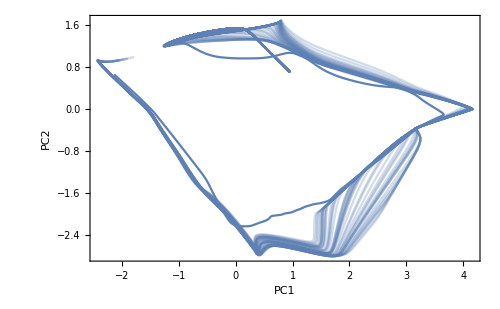

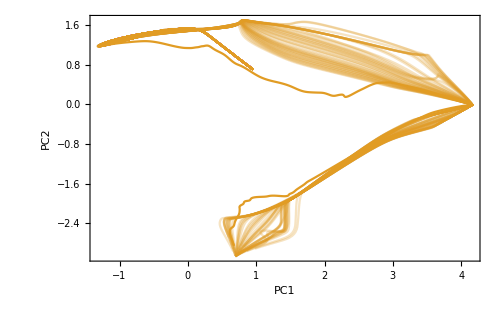

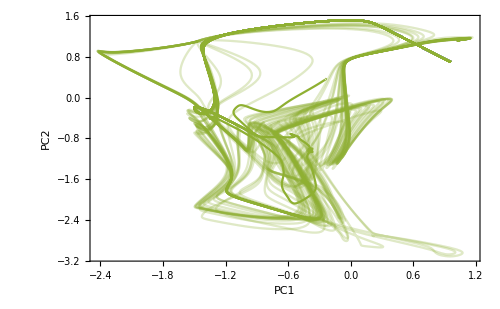

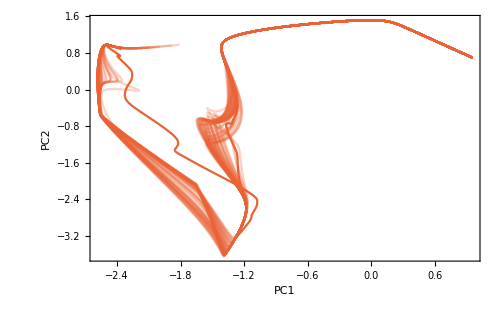

```mathematica
Show[{
ListLinePlot[ba,PlotStyle->Directive[Opacity[0.15],cd[[1]]]],
ListLinePlot[baM,PlotStyle->cd[[1]]],
ListLinePlot[{ba[[1]][[1]]},PlotStyle->Black]
},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"PC1","PC2"},ImageSize->500]

Show[{
ListLinePlot[bc,PlotStyle->Directive[Opacity[0.15],cd[[2]]]],
ListLinePlot[bcM,PlotStyle->cd[[2]]],
ListLinePlot[{bc[[1]][[1]]},PlotStyle->Black]
},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"PC1","PC2"},ImageSize->500]

Show[{
ListLinePlot[aa,PlotStyle->Directive[Opacity[0.15],cd[[3]]]],
ListLinePlot[aaM,PlotStyle->cd[[3]]],
ListLinePlot[{aa[[1]][[1]]},PlotStyle->Black]
},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"PC1","PC2"},ImageSize->500]

Show[{
ListLinePlot[ac,PlotStyle->Directive[Opacity[0.15],cd[[4]]]],
ListLinePlot[acM,PlotStyle->cd[[4]]],
ListLinePlot[{ac[[1]][[1]]},PlotStyle->Black]
},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"PC1","PC2"},ImageSize->500]
```

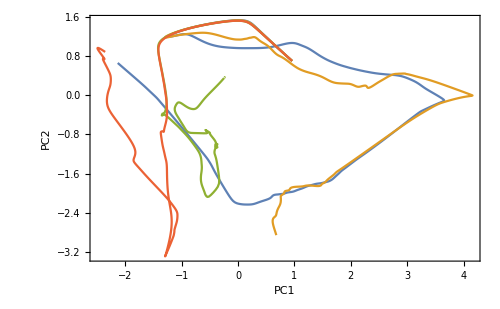

```mathematica
Show[{
ListLinePlot[baM,PlotStyle->cd[[1]]],
ListLinePlot[bcM,PlotStyle->cd[[2]]],
ListLinePlot[aaM,PlotStyle->cd[[3]]],
ListLinePlot[acM,PlotStyle->cd[[4]]],
ListLinePlot[{ba[[1]][[1]]},PlotStyle->Black]
},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"PC1","PC2"},ImageSize->500]
```

```mathematica
Show[{
ListLinePlot[ba,PlotStyle->Directive[Opacity[0.15],cd[[1]]]],
ListLinePlot[bc,PlotStyle->Directive[Opacity[0.15],cd[[2]]]],
ListLinePlot[aa,PlotStyle->Directive[Opacity[0.15],cd[[3]]]],
ListLinePlot[ac,PlotStyle->Directive[Opacity[0.15],cd[[4]]]],
ListLinePlot[{ba[[1]][[1]]},PlotStyle->Black]
},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"PC1","PC2"},ImageSize->500]
```

-Graphics-

## Dimension Reduction 3D

```mathematica
dr=DimensionReduction[vectors,3];
```

```mathematica
ba = Table[dr[Transpose[{ba1[[x]],ba2[[x]],ba3[[x]],ba4[[x]],ba5[[x]],ba6[[x]],ba7[[x]]}]],{x,1,100}];
bc = Table[dr[Transpose[{bc1[[x]],bc2[[x]],bc3[[x]],bc4[[x]],bc5[[x]],bc6[[x]],bc7[[x]]}]],{x,1,100}];
aa=Table[dr[Transpose[{aa1[[x]],aa2[[x]],aa3[[x]],aa4[[x]],aa5[[x]],aa6[[x]],aa7[[x]]}]],{x,1,100}];
ac = Table[dr[Transpose[{ac1[[x]],ac2[[x]],ac3[[x]],ac4[[x]],ac5[[x]],ac6[[x]],ac7[[x]]}]],{x,1,100}];
```

```mathematica
Graphics3D[{cd[[1]],Line[ba],cd[[2]],Line[bc],cd[[3]],Line[aa],cd[[4]],Line[ac]}]
```

-Graphics3D-